# Zero Temperature Potential

```mathematica
ClearAll["Global`*"]
```

## Fixed parameters

```mathematica
g=0.65;
gX=0.432371;
yt=0.7;
vR=15000;
yN=0.65;
```

## Tree level

```mathematica
V′tree[λ_,ϕ_]:=1/4 λ(ϕ^2-vR^2)^2;
```

## Mass spectrum

```mathematica
mWsq[ϕ_]:=(g^2 ϕ^2)/4;
mZsq[ϕ_]:=((g^2+gX^2)ϕ^2)/4;
mtsq[ϕ_]:=(yt^2 ϕ^2)/2;
mNsq[ϕ_]:=yN^2 ϕ^2/2;
mHsq[λ_,ϕ_]:=3λ ϕ^2-λ vR^2;
mXsq[λ_,ϕ_]:=λ ϕ^2-λ vR^2;
```

## CW

```mathematica
V′CW=1/(64 π^2)(mHsq[ϕ]^2(Log[mHsq[ϕ]/μ^2]-3/2)+3 mXsq[ϕ]^2(Log[mXsq[ϕ]/μ^2]-3/2)+6 mWsq[ϕ]^2(Log[mWsq[ϕ]^2/μ^2]-5/6)+3 mZsq[ϕ]^2(Log[mZsq[ϕ]/μ^2]-5/6)-12 mtsq[ϕ]^2(Log[mtsq[ϕ]/μ^2]-3/2))//Simplify;
```

## Try some benchmarks

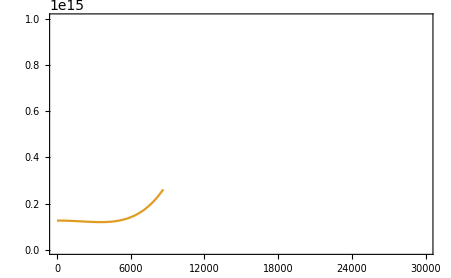

```mathematica
tree′level′setting={λ->0.01};
CW′level′setting={g->0.65,gX->0.432371,yt->0.9945};
renormscale={μ->10vR};
fix′energy′scale={vR->15000.};
V′tree′N=V′tree/.tree′level′setting/.fix′energy′scale;
V′CW′N=V′CW/.tree′level′setting/.CW′level′setting/.renormscale/.fix′energy′scale;
Plot[{V′tree′N,V′tree′N+Re[V′CW′N]},{ϕ,0,30000}]
```

## Fix the vev

```mathematica
B[λ_,ϕ_]:=1/(64 π^2 vR^4)(6 mWsq[vR]^2+3 mZsq[vR]^2+mHsq[λ,vR]^2-12 mtsq[vR]^2-8 mNsq[vR]^2);
V′B[λ_,ϕ_]:=2B[λ,ϕ] vR^2 ϕ^2-3/2 B[λ,ϕ] ϕ^4+B[λ,ϕ] ϕ^4 Log[ϕ^2/vR^2];
V′0T[λ_,ϕ_]:=V′tree[λ,ϕ]+V′B[λ,ϕ]-(V′tree[λ,10^-3]+V′B[λ,10^-3])
```

```mathematica
Plot[V′0T[0.009,ϕ],{ϕ,0,3.5vR}]
```

-Graphics-